# Proggetto Automatica-Traccia 29 Luca Timpano 240236

## Tempo Continuo

```mathematica
ClearAll["Global *"]
```

### Dati

```mathematica
A = {{-1225/2,1198,1076,2883/2},
{1227/2,-1196,-1077,-2887/2},
{-3675/2,3591,3229,8657/2},
{1225/2,-1197,-1076,-2885/2}}
B = {{1/2},{-1/2},{3/2},{-1/2}}
C1 = {{-5/2,-5/2,-5/2,-15/2}}
MatrixForm[A]
MatrixForm[B]
MatrixForm[C1]
```

{{-1225/2,1198,1076,2883/2},{1227/2,-1196,-1077,-2887/2},{-3675/2,3591,3229,8657/2},{1225/2,-1197,-1076,-2885/2}}

{{1/2},{-1/2},{3/2},{-1/2}}

{{-5/2,-5/2,-5/2,-15/2}}

(-1225/2 | 1198 | 1076 | 2883/2
1227/2 | -1196 | -1077 | -2887/2
-3675/2 | 3591 | 3229 | 8657/2
1225/2 | -1197 | -1076 | -2885/2)

(1/2
-1/2
3/2
-1/2)

(-5/2 | -5/2 | -5/2 | -15/2)

```mathematica
Subscript[x, 0]={{0},{-2},{-1},{1}}
```

{{0},{-2},{-1},{1}}

### Modi naturali

#### Polinomio Caratteristico

```mathematica
CharacteristicPolynomial[A,x]
```

2176+928 x+194 x^2+22 x^3+x^4

```mathematica
Simplify[A.A.A.A + 22 A.A.A + 194 A.A + 928 A + 2176 IdentityMatrix[4]]
```

{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}

#### Autovalori

```mathematica
λ = Eigenvalues[A]
```

{-8,-8,-3+5 ⅈ,-3-5 ⅈ}

#### Molteplicità Geometrica

```mathematica
NullSpace[A-(-8)IdentityMatrix[4]]
```

{{-623/639,511/639,-25/9,1}}

```mathematica
NullSpace[A-(-3+5ⅈ)IdentityMatrix[4]]
```

{{-1203/1189+(390 ⅈ)/8323,6667/8323-(1660 ⅈ)/8323,-115/41+(10 ⅈ)/41,1}}

```mathematica
NullSpace[A-(-3+5ⅈ)IdentityMatrix[4]]
```

{{-1203/1189+(390 ⅈ)/8323,6667/8323-(1660 ⅈ)/8323,-115/41+(10 ⅈ)/41,1}}

#### Polinomio minimo

```mathematica
MatrixMinimalPolynomial[a_List?MatrixQ,x_]:=Module[{i,n=1,qu={},mnm={Flatten[IdentityMatrix[Length[a]]]}},While[Length[qu]==0,AppendTo[mnm,Flatten[MatrixPower[a,n]]];
qu=NullSpace[Transpose[mnm]];
n++];
First[qu].Table[x^i,{i,0,n-1}]]
```

```mathematica
MatrixMinimalPolynomial[A,x]
```

2176+928 x+194 x^2+22 x^3+x^4

#### Matrice di Jordan

```mathematica
{T,Λ}  = JordanDecomposition[A]
```

{{{-623/639,2306/408321,-1203/1189-(390 ⅈ)/8323,-1203/1189+(390 ⅈ)/8323},{511/639,-8224/408321,6667/8323+(1660 ⅈ)/8323,6667/8323-(1660 ⅈ)/8323},{-25/9,2/81,-115/41-(10 ⅈ)/41,-115/41+(10 ⅈ)/41},{1,0,1,1}},{{-8,1,0,0},{0,-8,0,0},{0,0,-3-5 ⅈ,0},{0,0,0,-3+5 ⅈ}}}

```mathematica
T // MatrixForm
```

(-623/639 | 2306/408321 | -1203/1189-(390 ⅈ)/8323 | -1203/1189+(390 ⅈ)/8323
511/639 | -8224/408321 | 6667/8323+(1660 ⅈ)/8323 | 6667/8323-(1660 ⅈ)/8323
-25/9 | 2/81 | -115/41-(10 ⅈ)/41 | -115/41+(10 ⅈ)/41
1 | 0 | 1 | 1)

```mathematica
Λ // MatrixForm
```

(-8 | 1 | 0 | 0
0 | -8 | 0 | 0
0 | 0 | -3-5 ⅈ | 0
0 | 0 | 0 | -3+5 ⅈ)

```mathematica
MatrixForm[MatrixExp[Λ t]]
```

(ⅇ^(-8 t) | ⅇ^(-8 t) t | 0 | 0
0 | ⅇ^(-8 t) | 0 | 0
0 | 0 | ⅇ^((-3-5 ⅈ) t) | 0
0 | 0 | 0 | ⅇ^((-3+5 ⅈ) t))

#### Modi Naturali

```mathematica
M = {ⅇ^(-8 t),ⅇ^(-8 t) t,ⅇ^(-3t)Cos[-5t],ⅇ^(-3t)Sin[5t]}
```

{ⅇ^(-8 t),ⅇ^(-8 t) t,ⅇ^(-3 t) Cos[5 t],ⅇ^(-3 t) Sin[5 t]}

#### Grafico

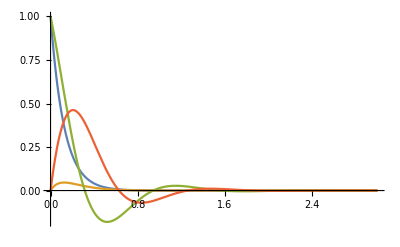

```mathematica
Plot[M,{t,0,3},PlotRange->Full]
```

### Risposta Libera

```mathematica
Subscript[z, 0] = Inverse[T].Subscript[x, 0]
```

{{-35711/500},{161667/50},{36211/1000-(31199 ⅈ)/200},{36211/1000+(31199 ⅈ)/200}}

```mathematica
Subscript[z, 0] // MatrixForm
```

(-35711/500
161667/50
36211/1000-(31199 ⅈ)/200
36211/1000+(31199 ⅈ)/200)

#### Calcolo la risposta libera

```mathematica
Subscript[x1, l][t_] := Expand[T.MatrixExp[Λ t].Subscript[z, 0]]
```

```mathematica
Subscript[x1, l][t] // MatrixForm
```

((43947 ⅇ^(-8 t))/500-(43947/1000-(31227 ⅈ)/200) ⅇ^((-3-5 ⅈ) t)-(43947/1000+(31227 ⅈ)/200) ⅇ^((-3+5 ⅈ) t)-157619/50 ⅇ^(-8 t) t
-61119/500 ⅇ^(-8 t)+(60119/1000-(23547 ⅈ)/200) ⅇ^((-3-5 ⅈ) t)+(60119/1000+(23547 ⅈ)/200) ⅇ^((-3+5 ⅈ) t)+129283/50 ⅇ^(-8 t) t
(27823 ⅇ^(-8 t))/100-(27923/200-(85743 ⅈ)/200) ⅇ^((-3-5 ⅈ) t)-(27923/200+(85743 ⅈ)/200) ⅇ^((-3+5 ⅈ) t)-17963/2 ⅇ^(-8 t) t
-35711/500 ⅇ^(-8 t)+(36211/1000-(31199 ⅈ)/200) ⅇ^((-3-5 ⅈ) t)+(36211/1000+(31199 ⅈ)/200) ⅇ^((-3+5 ⅈ) t)+161667/50 ⅇ^(-8 t) t)

#### Grafico

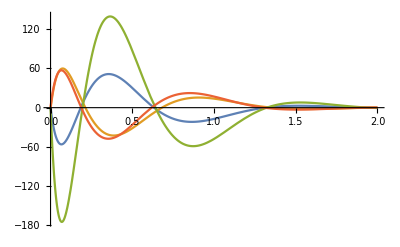

```mathematica
Plot[{{(43947 ⅇ^(-8 t))/500-(43947/1000-(31227 ⅈ)/200) ⅇ^((-3-5 ⅈ) t)-(43947/1000+(31227 ⅈ)/200) ⅇ^((-3+5 ⅈ) t)-157619/50 ⅇ^(-8 t) t}, {-61119/500 ⅇ^(-8 t)+(60119/1000-(23547 ⅈ)/200) ⅇ^((-3-5 ⅈ) t)+(60119/1000+(23547 ⅈ)/200) ⅇ^((-3+5 ⅈ) t)+129283/50 ⅇ^(-8 t) t}, {(27823 ⅇ^(-8 t))/100-(27923/200-(85743 ⅈ)/200) ⅇ^((-3-5 ⅈ) t)-(27923/200+(85743 ⅈ)/200) ⅇ^((-3+5 ⅈ) t)-17963/2 ⅇ^(-8 t) t}, {-35711/500 ⅇ^(-8 t)+(36211/1000-(31199 ⅈ)/200) ⅇ^((-3-5 ⅈ) t)+(36211/1000+(31199 ⅈ)/200) ⅇ^((-3+5 ⅈ) t)+161667/50 ⅇ^(-8 t) t}},{t,0,2},PlotRange->All]
```

#### Risposta libera Laplace

```mathematica
Subscript[x2, l]=InverseLaplaceTransform[Inverse[s IdentityMatrix[4]-A].Subscript[x, 0],s,t]
```

{{(43947 ⅇ^(-8 t))/500-(3 ⅇ^((-3-5 ⅈ) t) ((14649-52045 ⅈ)+(14649+52045 ⅈ) ⅇ^(10 ⅈ t)))/1000-157619/50 ⅇ^(-8 t) t},{-61119/500 ⅇ^(-8 t)+(ⅇ^((-3-5 ⅈ) t) ((60119-117735 ⅈ)+(60119+117735 ⅈ) ⅇ^(10 ⅈ t)))/1000+129283/50 ⅇ^(-8 t) t},{(27823 ⅇ^(-8 t))/100-7/200 ⅇ^((-3-5 ⅈ) t) ((3989-12249 ⅈ)+(3989+12249 ⅈ) ⅇ^(10 ⅈ t))-17963/2 ⅇ^(-8 t) t},{-35711/500 ⅇ^(-8 t)+(7 ⅇ^((-3-5 ⅈ) t) ((5173-22285 ⅈ)+(5173+22285 ⅈ) ⅇ^(10 ⅈ t)))/1000+161667/50 ⅇ^(-8 t) t}}

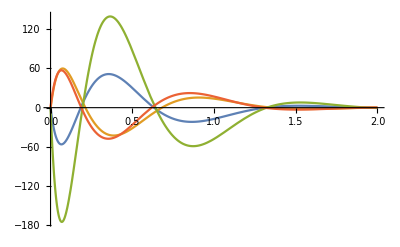

```mathematica
Plot[Subscript[x2, l],{t,0,2},PlotRange->All]
```

#### Risposta libera nell’uscita

```mathematica
yl[t_]=Expand[Simplify[C1.Subscript[x1, l][t]]]
```

{{-1481/20 ⅇ^(-8 t)+(1481/40+(87 ⅈ)/40) ⅇ^((-3-5 ⅈ) t)+(1481/40-(87 ⅈ)/40) ⅇ^((-3+5 ⅈ) t)-759/2 ⅇ^(-8 t) t}}

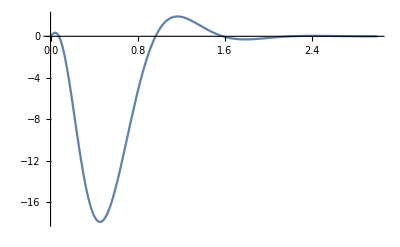

```mathematica
Plot[yl[t],{t,0,3},PlotRange->All]
```

### Configurazione degli stati iniziali

```mathematica
T // MatrixForm
```

(-623/639 | 2306/408321 | -1203/1189-(390 ⅈ)/8323 | -1203/1189+(390 ⅈ)/8323
511/639 | -8224/408321 | 6667/8323+(1660 ⅈ)/8323 | 6667/8323-(1660 ⅈ)/8323
-25/9 | 2/81 | -115/41-(10 ⅈ)/41 | -115/41+(10 ⅈ)/41
1 | 0 | 1 | 1)

```mathematica
x1 = 1/8*Transpose[T][[1]]
```

{-623/5112,511/5112,-25/72,1/8}

```mathematica
Subscript[x, l1] [t_]:=Expand[MatrixExp[A t].x1]
```

```mathematica
Subscript[x, l1] [t] // MatrixForm
```

(-(623 ⅇ^(-8 t))/5112
(511 ⅇ^(-8 t))/5112
-25/72 ⅇ^(-8 t)
ⅇ^(-8 t)/8)

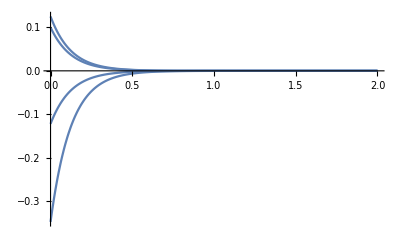

```mathematica
Plot[{Subscript[x, l1][t]},{t,0,2},PlotRange->All]
```

```mathematica
x2 = 1/8*Transpose[T][[2]]
```

{1153/1633284,-1028/408321,1/324,0}

```mathematica
Subscript[x, l2] [t_]:=Expand[MatrixExp[A t].x2]
```

```mathematica
Subscript[x, l2] [t] // MatrixForm
```

((1153 ⅇ^(-8 t))/1633284-(623 ⅇ^(-8 t) t)/5112
-(1028 ⅇ^(-8 t))/408321+(511 ⅇ^(-8 t) t)/5112
ⅇ^(-8 t)/324-25/72 ⅇ^(-8 t) t
1/8 ⅇ^(-8 t) t)

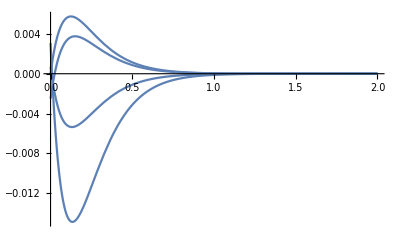

```mathematica
Plot[{Subscript[x, l2][t]},{t,0,2},PlotRange->All]
```

```mathematica
x3 = 1/8*Transpose[T][[3]]
```

{-1203/9512-(195 ⅈ)/33292,6667/66584+(415 ⅈ)/16646,-115/328-(5 ⅈ)/164,1/8}

```mathematica
Subscript[x, l3] [t_]:=Expand[MatrixExp[A t].x3]
```

```mathematica
Subscript[x, l3] [t] // MatrixForm
```

((-1203/9512-(195 ⅈ)/33292) ⅇ^((-3-5 ⅈ) t)
(6667/66584+(415 ⅈ)/16646) ⅇ^((-3-5 ⅈ) t)
(-115/328-(5 ⅈ)/164) ⅇ^((-3-5 ⅈ) t)
1/8 ⅇ^((-3-5 ⅈ) t))

```mathematica
x13real[t_]:=ComplexExpand[Re[Subscript[x, l3][t]]]
```

```mathematica
x13real [t] // MatrixForm
```

(-(1203 ⅇ^(-3 t) Cos[5 t])/9512-(195 ⅇ^(-3 t) Sin[5 t])/33292
(6667 ⅇ^(-3 t) Cos[5 t])/66584+(415 ⅇ^(-3 t) Sin[5 t])/16646
-115/328 ⅇ^(-3 t) Cos[5 t]-5/164 ⅇ^(-3 t) Sin[5 t]
1/8 ⅇ^(-3 t) Cos[5 t])

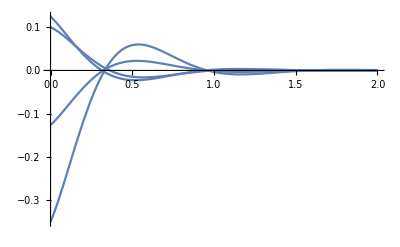

```mathematica
Plot[{x13real[t]},{t,0,2},PlotRange->All]
```

### Funzione di Trasferimento

```mathematica
G[s_]:=Simplify[C1.Inverse[s IdentityMatrix[4]-A].B]⟦1,1⟧
```

```mathematica
G[s]
```

(5 (1+2 s))/(2 (8+s)^2 (34+6 s+s^2))

#### Zeri

```mathematica
Solve[Numerator[G[s]]== 0,s]
```

{{s→-1/2}}

#### Poli

```mathematica
Solve[Denominator[G[s]]== 0,s]
```

{{s→-8},{s→-8},{s→-3-5 ⅈ},{s→-3+5 ⅈ}}

### Risposta al Gradino Unitario

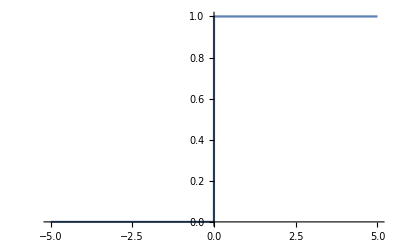

```mathematica
Plot[{UnitStep[t]},{t,-5,5}, PlotRange->All]
```

```mathematica
Subscript[Y, f][s_]:=G[s]/s
```

```mathematica
Subscript[Y, f][s]
```

(5 (1+2 s))/(2 s (8+s)^2 (34+6 s+s^2))

#### Risposta Forzata con InverseLaplaceTransform

```mathematica
Expand[Simplify[ComplexExpand[InverseLaplaceTransform[Subscript[Y, f][s],s,t]]]]
```

5/4352+(23 ⅇ^(-8 t))/1280+3/32 ⅇ^(-8 t) t-13/680 ⅇ^(-3 t) Cos[5 t]-1/680 ⅇ^(-3 t) Sin[5 t]

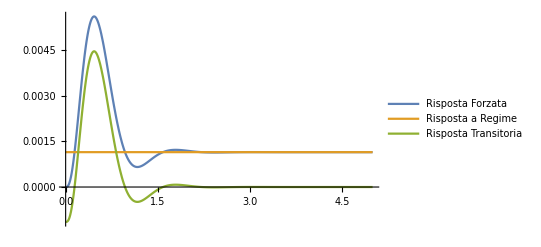

```mathematica
Plot[{5/4352+(23 ⅇ^(-8 t))/1280+3/32 ⅇ^(-8 t) t-13/680 ⅇ^(-3 t) Cos[5 t]-1/680 ⅇ^(-3 t) Sin[5 t],5/4352,(23 ⅇ^(-8 t))/1280+3/32 ⅇ^(-8 t) t-13/680 ⅇ^(-3 t) Cos[5 t]-1/680 ⅇ^(-3 t) Sin[5 t]},{t,0,5},PlotRange->All,PlotLegends->{"Risposta Forzata","Risposta a Regime","Risposta Transitoria"}]
```

#### Risposta Forzata con la scomposizione in fratti semplici

```mathematica
Apart[Subscript[Y, f][s]]
```

5/(4352 s)+3/(32 (8+s)^2)+23/(1280 (8+s))+(-44-13 s)/(680 (34+6 s+s^2))

Scrivo manualmente la scomposizione

```mathematica
Subscript[C, 1](1/s)+Subscript[C, 21](1/(s+8))+Subscript[C, 22](1/(s+8)^2)+Subscript[C, 3](1/(s+3-5 ⅈ))+Subscript[C, 4](1/(s+3+5 ⅈ))
```

C_1/s+C_3/((3-5 ⅈ)+s)+C_4/((3+5 ⅈ)+s)+C_21/(8+s)+C_22/(8+s)^2

```mathematica
Subscript[C, 1]=G[0]
```

5/4352

#### Formula di Heaviside

```mathematica
Subscript[C, 22] = lim_(s->-8) (s+8)^2 Subscript[Y, f][s]
```

3/32

```mathematica
Subscript[C, 21]= lim_(s->-8) D[(s+8)^2 Subscript[Y, f][s],s]
```

23/1280

```mathematica
Subscript[C, 3]= lim_(s->-3+5 ⅈ) (s+3-5 ⅈ)Subscript[Y, f][s]
```

-13/1360+ⅈ/1360

```mathematica
Subscript[C, 4] = Conjugate[Subscript[C, 3]]
```

-13/1360-ⅈ/1360

```mathematica
Subscript[C, 1](1/s)+Subscript[C, 21](1/(s+8))+Subscript[C, 22](1/(s+8)^2)+Subscript[C, 3](1/(s+3-5 ⅈ))+Subscript[C, 4](1/(s+3+5 ⅈ))
```

5/(4352 s)-(13/1360-ⅈ/1360)/((3-5 ⅈ)+s)-(13/1360+ⅈ/1360)/((3+5 ⅈ)+s)+3/(32 (8+s)^2)+23/(1280 (8+s))

```mathematica
F[Z_,γ_,t_]:=ComplexExpand[Re[Z Exp[I γ t]]]
```

```mathematica
Subscript[y, f][t_]:=Subscript[C, 1] UnitStep[t]+Subscript[C, 21] Exp[-8 t]UnitStep[t]+Subscript[C, 22] t Exp[-8 t]UnitStep[t]+2 Exp[-3t]F[Subscript[C, 3],5,t]UnitStep[t]
```

```mathematica
Subscript[y, f][t]
```

(5 UnitStep[t])/4352+(23 ⅇ^(-8 t) UnitStep[t])/1280+3/32 ⅇ^(-8 t) t UnitStep[t]+2 ⅇ^(-3 t) (-(13 Cos[5 t])/1360-Sin[5 t]/1360) UnitStep[t]

#### Grafico

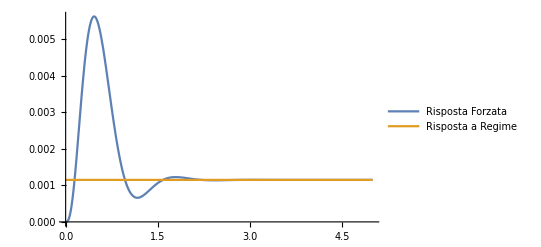

```mathematica
Plot[{Subscript[y, f][t],5/4352},{t,0,5},PlotRange->All,PlotLegends->{"Risposta Forzata","Risposta a Regime"}]
```

### Risposta al Segnale Periodico Elementare

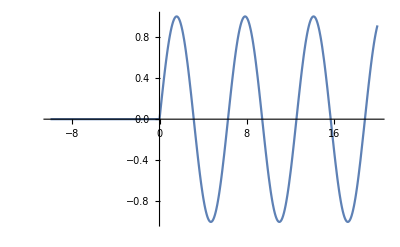

```mathematica
Plot[{Sin[t]UnitStep[t]},{t,-10,20}, PlotRange->All]
```

```mathematica
U[s_]:=LaplaceTransform[Sin[t] UnitStep[t],t,s]
```

```mathematica
U[s]
```

1/(1+s^2)

```mathematica
Subscript[Y, f2][s_]:= G[s]U[s]
```

```mathematica
Subscript[Y, f2][s]
```

(5 (1+2 s))/(2 (8+s)^2 (1+s^2) (34+6 s+s^2))

```mathematica
Apart[Subscript[Y, f2][s]]
```

-3/(260 (8+s)^2)-61/(16900 (8+s))+(253+204 s)/(126750 (1+s^2))+(-11+3 s)/(1500 (34+6 s+s^2))

#### Fratti semplici

```mathematica
Expand[Simplify[Subscript[C, 1](1/(s + ⅈ))+Subscript[C, 2](1/(s - ⅈ))+Subscript[C, 31](1/(s+8))+Subscript[C, 32](1/(s+8)^2)+Subscript[C, 4](1/(s+3-5 ⅈ))+Subscript[C, 5](1/(s+3+5 ⅈ))]]
```

5/(4352 (ⅈ+s))-(13/1360+ⅈ/1360)/((3-5 ⅈ)+s)+C_2/(-ⅈ+s)+C_5/((3+5 ⅈ)+s)+C_31/(8+s)+C_32/(8+s)^2

#### Formula di Heaviside

```mathematica
Subscript[C, 1]= lim_(s->-ⅈ) (s + ⅈ)Subscript[Y, f2][s]
```

17/21125+(253 ⅈ)/253500

```mathematica
Subscript[C, 2]= lim_(s->ⅈ) (s - ⅈ)Subscript[Y, f2][s]
```

17/21125-(253 ⅈ)/253500

```mathematica
Subscript[C, 32]= lim_(s->-8) (s + 8)^2 Subscript[Y, f2][s]
```

-3/260

```mathematica
Subscript[C, 31]= lim_(s->-8) D[(s + 8)^2 Subscript[Y, f2][s],s]
```

-61/16900

```mathematica
Subscript[C, 4]= lim_(s->-3+5ⅈ) (s + 3-5ⅈ)Subscript[Y, f2][s]
```

1/1000+ⅈ/750

```mathematica
Subscript[C, 5] = Conjugate[Subscript[C, 4]]
```

1/1000-ⅈ/750

```mathematica
Subscript[C, 1](1/(s + ⅈ))+Subscript[C, 2](1/(s-ⅈ))+Subscript[C, 31](1/(s+8))+Subscript[C, 32](1/(s+8)^2)+Subscript[C, 4](1/(s+3-5 ⅈ))+Subscript[C, 5](1/(s+3+5 ⅈ))
```

(17/21125-(253 ⅈ)/253500)/(-ⅈ+s)+(17/21125+(253 ⅈ)/253500)/(ⅈ+s)+(1/1000+ⅈ/750)/((3-5 ⅈ)+s)+(1/1000-ⅈ/750)/((3+5 ⅈ)+s)-3/(260 (8+s)^2)-61/(16900 (8+s))

#### Risposta forzata

```mathematica
Subscript[y, f2][t_]:=Subscript[C, 1] Exp[-ⅈ t]UnitStep[t]+Subscript[C, 2] Exp[ⅈ t]UnitStep[t]+Subscript[C, 31] Exp[-8 t]UnitStep[t]+Subscript[C, 32] t Exp[-8 t]UnitStep[t]+2 Exp[-3t]F[Subscript[C, 3],5,t]UnitStep[t]
```

```mathematica
Subscript[y, f2][t]
```

-(61 ⅇ^(-8 t) UnitStep[t])/16900+(17/21125+(253 ⅈ)/253500) ⅇ^(-ⅈ t) UnitStep[t]+(17/21125-(253 ⅈ)/253500) ⅇ^(ⅈ t) UnitStep[t]-3/260 ⅇ^(-8 t) t UnitStep[t]+2 ⅇ^(-3 t) (-(13 Cos[5 t])/1360-Sin[5 t]/1360) UnitStep[t]

```mathematica
Expand[InverseLaplaceTransform[Subscript[Y, f2][s],s,t]]
```

-(61 ⅇ^(-8 t))/16900+(1/1000-ⅈ/750) ⅇ^((-3-5 ⅈ) t)+(1/1000+ⅈ/750) ⅇ^((-3+5 ⅈ) t)-3/260 ⅇ^(-8 t) t+(34 Cos[t])/21125+(253 Sin[t])/126750

#### Risposta a regime

```mathematica
Subscript[y, f2reg][t_]:=2 ComplexExpand[Re[Subscript[C, 2] Exp[I t]]]
```

```mathematica
Expand[Subscript[y, f2reg][t]]
```

(34 Cos[t])/21125+(253 Sin[t])/126750

#### Risposta transitoria

```mathematica
Subscript[y, transitoria][t_] := -(61 ⅇ^(-8 t))/16900+(1/1000-ⅈ/750) ⅇ^((-3-5 ⅈ) t)+(1/1000+ⅈ/750) ⅇ^((-3+5 ⅈ) t)-3/260 ⅇ^(-8 t) t
```

```mathematica
Subscript[y, transitoria][t]
```

-(61 ⅇ^(-8 t))/16900+(1/1000-ⅈ/750) ⅇ^((-3-5 ⅈ) t)+(1/1000+ⅈ/750) ⅇ^((-3+5 ⅈ) t)-3/260 ⅇ^(-8 t) t

#### Grafico

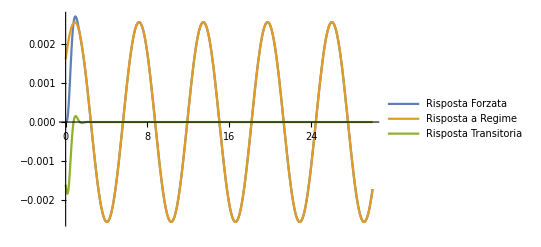

```mathematica
Plot[{-(61 ⅇ^(-8 t))/16900+(1/1000-ⅈ/750) ⅇ^((-3-5 ⅈ) t)+(1/1000+ⅈ/750) ⅇ^((-3+5 ⅈ) t)-3/260 ⅇ^(-8 t) t+(34 Cos[t])/21125+(253 Sin[t])/126750,(34 Cos[t])/21125+(253 Sin[t])/126750,-(61 ⅇ^(-8 t))/16900+(1/1000-ⅈ/750) ⅇ^((-3-5 ⅈ) t)+(1/1000+ⅈ/750) ⅇ^((-3+5 ⅈ) t)-3/260 ⅇ^(-8 t) t},{t,0,30},PlotRange->All,PlotLegends->{"Risposta Forzata","Risposta a Regime","Risposta Transitoria"}]
```

### Modello ARMA

```mathematica
G[s]
```

(5 (1+2 s))/(2 (8+s)^2 (34+6 s+s^2))

```mathematica
Num = Expand[Numerator[G[s]]]
```

5+10 s

```mathematica
Den = Expand[Denominator[G[s]]]
```

4352+1856 s+388 s^2+44 s^3+2 s^4

```mathematica
Subscript[G, ars][s_]:= Num/Den
```

```mathematica
Subscript[G, ars][s]
```

(5+10 s)/(4352+1856 s+388 s^2+44 s^3+2 s^4)

```mathematica
Expand[Denominator[Subscript[G, ars][s]] Y[s]==Numerator[Subscript[G, ars][s]] Subscript[U, 1][s]]
```

4352 Y[s]+1856 s Y[s]+388 s^2 Y[s]+44 s^3 Y[s]+2 s^4 Y[s]==5 U_1[s]+10 s U_1[s]

```mathematica
ARMA = InverseLaplaceTransform[4352 Y[s]+1856 s Y[s]+388 s^2 Y[s]+44 s^3 Y[s]+2 s^4 Y[s]==5 Subscript[U, 1][s]+10 s Subscript[U, 1][s], s,t]/.{Y[s]->LaplaceTransform[y[t],t,s], Subscript[U, 1][s]->LaplaceTransform[u[t],t,s]} /.{y[0]->0, y'[0]->0, y''[0]->0, y'''[0]->0}/.
{u[0] -> 0, u'[0] -> 0}
```

4352 y[t]+1856 y'[t]+388 y''[t]+44 y^(3)[t]+2 y^(4)[t]==5 u[t]+10 u'[t]

```mathematica
Subscript[x0, arma]= {{2},{-3},{3},{1}};
```

```mathematica
y0 = (C1[[1]].Subscript[x0, arma])[[1]]
```

-25/2

```mathematica
y0'=(C1[[1]].A.Subscript[x0, arma])[[1]]
```

25/2

```mathematica
y0''=(C1[[1]].A.A.Subscript[x0, arma])[[1]]
```

35

```mathematica
y0'''= (C1[[1]].A.A.A.Subscript[x0, arma])[[1]]
```

-2755/2

```mathematica
eqDiffL=Simplify[LaplaceTransform[ARMA,t, s]/.{LaplaceTransform[y[t],t,s]->Y[s],LaplaceTransform[u[t],t,s]->Subscript[U, 1][s],u[0]->0}]
```

2 (8+s)^2 (34+6 s+s^2) Y[s]==5 (1+2 s) U_1[s]+2 ((928+194 s+22 s^2+s^3) y[0]+(194+22 s+s^2) y'[0]+22 y''[0]+s y''[0]+y^(3)[0])

```mathematica
Ydif[s_]:=Collect[Solve[eqDiffL,Y[s]][[1,1]][[2]], Subscript[U, 1][s]]
```

```mathematica
Ydif[s]
```

((5+10 s) U_1[s])/(2 (8+s)^2 (34+6 s+s^2))+(1856 y[0]+388 s y[0]+44 s^2 y[0]+2 s^3 y[0]+388 y'[0]+44 s y'[0]+2 s^2 y'[0]+44 y''[0]+2 s y''[0]+2 y^(3)[0])/(2 (8+s)^2 (34+6 s+s^2))

```mathematica
Subscript[U, ru][s_]:=LaplaceTransform[t UnitStep[t],t,s]
```

```mathematica
Subscript[U, ru][s]
```

1/s^2

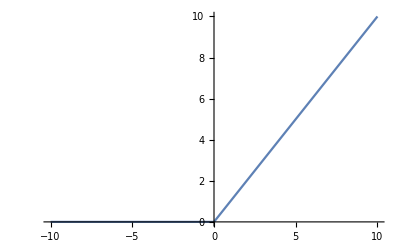

```mathematica
Plot[t UnitStep[t],{t,-10,10}, PlotRange->All]
```

```mathematica
Subscript[y, tot][s_]:=Ydif[s]/.
{y[0]->y0,y'[0]->y0',y''[0]->y0'',y'''[0]->y0'''}
```

```mathematica
Subscript[y, tot][s]
```

(-19565-4230 s-525 s^2-25 s^3)/(2 (8+s)^2 (34+6 s+s^2))+((5+10 s) U_1[s])/(2 (8+s)^2 (34+6 s+s^2))

```mathematica
Subscript[y, forzata][] = Expand[InverseLaplaceTransform[((5+10 s) Subscript[U, 1][s])/(2 (8+s)^2 (34+6 s+s^2))/.{Subscript[U, 1][s]->(1/s^2)},s,t]]
```

535/295936-(19 ⅇ^(-8 t))/5120+(11/11560-(31 ⅈ)/23120) ⅇ^((-3-5 ⅈ) t)+(11/11560+(31 ⅈ)/23120) ⅇ^((-3+5 ⅈ) t)+(5 t)/4352-3/256 ⅇ^(-8 t) t

Confronto

```mathematica
Subscript[Y, fr][s_]:=G[s]/s^2
```

```mathematica
Subscript[Y, fr][s]
```

(5 (1+2 s))/(2 s^2 (8+s)^2 (34+6 s+s^2))

```mathematica
Expand[InverseLaplaceTransform[Subscript[Y, fr][s],s,t]]
```

535/295936-(19 ⅇ^(-8 t))/5120+(11/11560-(31 ⅈ)/23120) ⅇ^((-3-5 ⅈ) t)+(11/11560+(31 ⅈ)/23120) ⅇ^((-3+5 ⅈ) t)+(5 t)/4352-3/256 ⅇ^(-8 t) t

### Stato

Rappresento il modello in “forma compatta” in una struttura StateSpaceModel

```mathematica
Σ=StateSpaceModel[{A,B,C1}]
```

-1225/2119810762883/21/21227/2-1196-1077-2887/2-1/2-3675/2359132298657/23/21225/2-1197-1076-2885/2-1/2-5/2-5/2-5/2-15/20StateSpaceModelFalseFalseFalseFalse$CellContext`stname1$CellContext`stname2$CellContext`stname3$CellContext`stname4Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$IdentityAutomatic1141FalseFalseFalseAutomaticNoneAutomatic

#### Funzione di trasferimento

```mathematica
G[s]
```

(5 (1+2 s))/(2 (8+s)^2 (34+6 s+s^2))

#### Autovalori

```mathematica
λ
```

{-8,-8,-3+5 ⅈ,-3-5 ⅈ}

#### Modi naturali

```mathematica
M
```

{ⅇ^(-8 t),ⅇ^(-8 t) t,ⅇ^(-3 t) Cos[5 t],ⅇ^(-3 t) Sin[5 t]}

#### Risposta libera

```mathematica
x0={{Subscript[x, 1]},{Subscript[x, 2]},{Subscript[x, 3]},{Subscript[x, 4]}}
```

{{x_1},{x_2},{x_3},{x_4}}

```mathematica
Subscript[Y, libera][s]=Simplify[C1.Inverse[s IdentityMatrix[4]-A].x0][[1]][[1]]
```

-(5 ((3619+218 s+23 s^2+s^3) x_1+(-3401+241 s+24 s^2+s^3) x_2-3425 x_3+192 s x_3+22 s^2 x_3+s^3 x_3-3253 x_4+557 s x_4+65 s^2 x_4+3 s^3 x_4))/(2 (8+s)^2 (34+6 s+s^2))

#### Risposta forzata al gradino, risposta a regime e transitoria

```mathematica
Subscript[Y, f][s]
```

(5 (1+2 s))/(2 s (8+s)^2 (34+6 s+s^2))

```mathematica
Subscript[Y, f-regime][s] = Simplify[G[0](1/s)]
```

5/(4352 s)

```mathematica
Subscript[Y, f-transitoria][s] =Simplify[Subscript[Y, f][s]-Subscript[Y, f-regime][s]]
```

(5 (-1+(2176 (1+2 s))/((8+s)^2 (34+6 s+s^2))))/(4352 s)

#### Stato inziale

```mathematica
x0={{Subscript[x, 1]},{Subscript[x, 2]},{Subscript[x, 3]},{Subscript[x, 4]}}
```

{{x_1},{x_2},{x_3},{x_4}}

```mathematica
Numerator[Simplify[Expand[Subscript[Y, libera][s]+Subscript[Y, f-transitoria][s]]]]
```

-5 (-3424+194 s+22 s^2+s^3+2176 (3619+218 s+23 s^2+s^3) x_1+2176 (-3401+241 s+24 s^2+s^3) x_2-7452800 x_3+417792 s x_3+47872 s^2 x_3+2176 s^3 x_3-7078528 x_4+1212032 s x_4+141440 s^2 x_4+6528 s^3 x_4)

```mathematica
CoefficientList[Numerator[Simplify[Expand[Subscript[Y, libera][s]+Subscript[Y, f-transitoria][s]]]],s]
```

{17120-39374720 x_1+37002880 x_2+37264000 x_3+35392640 x_4,-970-2371840 x_1-2622080 x_2-2088960 x_3-6060160 x_4,-110-250240 x_1-261120 x_2-239360 x_3-707200 x_4,-5-10880 x_1-10880 x_2-10880 x_3-32640 x_4}

```mathematica
Solve[CoefficientList[Numerator[Simplify[Expand[Subscript[Y, libera][s]+Subscript[Y, f-transitoria][s]]]],s]=={0,0,0,0},{Subscript[x, 1],Subscript[x, 2],Subscript[x, 3],Subscript[x, 4]}]
```

{{x_1→1/4352,x_2→-1/4352,x_3→1/4352,x_4→-1/4352}}

```mathematica
OutputResponse[{Σ,{1/4352,-1/4352,1/4352,-1/4352}},1,t]
```

{5/4352}

### Segnale

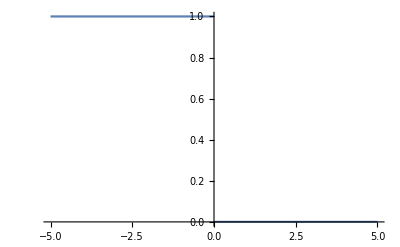

```mathematica
Plot[{UnitStep[-t]},{t,-5,5}, PlotRange->All]
```

```mathematica
G[s]
```

(5 (1+2 s))/(2 (8+s)^2 (34+6 s+s^2))

```mathematica
Subscript[y, neg] = G[0]
```

5/4352

```mathematica
MO={C1[[1]],(C1.A)[[1]],(C1.A.A)[[1]],(C1.A.A.A)[[1]]}
```

{{-5/2,-5/2,-5/2,-15/2},{-5/2,-5,0,5/2},{-5,-15/2,5,15/2},{-12265/2,23915/2,21545/2,28885/2}}

```mathematica
Det[MO]
```

17578125/8

```mathematica
Subscript[x, 01]=Inverse[MO].{{G[0]},{0},{0},{0}}
```

{{-19747/122400000},{2339/122400000},{1273/24480000},{-5023/40800000}}

```mathematica
Subscript[Y, l]=Apart[Simplify[(C1.Inverse[s IdentityMatrix[4]-A].Subscript[x, 01])[[1]][[1]]]]
```

1/(160 (8+s)^2)+13/(6400 (8+s))+(16-3 s)/(3400 (34+6 s+s^2))

```mathematica
Subscript[y, l] = Expand[Simplify[ComplexExpand[InverseLaplaceTransform[yliberas,s,t]]]]
```

yliberas DiracDelta[t]

```mathematica
Subscript[y, tot][t_]:=Piecewise[{{Subscript[y, neg], t<0}, {Subscript[y, l], t>=0}}]
```

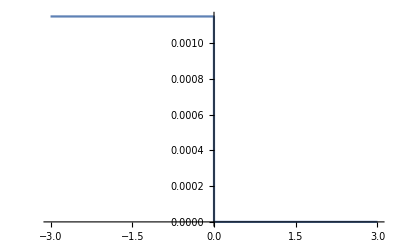

```mathematica
Plot[Subscript[y, tot][t],{t,-3,3},PlotRange->All]
```